## Setup

#### Beam splitter transformation

```mathematica
B[r_,t_]={{t,-r},{r,t}};
```

```mathematica
(* Creation operators are representated by c *)
```

#### First beam splitter

```mathematica
{ca0,cb0}=B[1/(√2),1/(√2)].{ca1,cb1};
```

#### Phase shift in lower path

```mathematica
cb1=ⅇ^(-ⅈ ϕ)cb2;
```

#### Second and ‘Fourth’ beam splitters

```mathematica
{ca1,cc1}=B[𝓇,𝓉].{ca2,cc2};
{cb2,cd1}=B[𝓇,𝓉].{cb3,cd2};
```

#### Third beam splitter

```mathematica
{cc2,cd2}=B[1/(√2),1/(√2)].{cc3,cd3};
```

## 1. Single-Mode Squeezed Vacuum

### SMSV in mode a

```mathematica
ClearAll[S,out]
S[ξ_,n_]=1/(√Cosh[ξ])∑_(k=0)^n √Binomial[2k,k](-Tanh[ξ]/2)^k ca0^(2k)/(√((2k)!)); (* Source: Wikipedia*)
(* S[ξ,n] approximates single mode squeezed vacuum up to photon number = 2n *)
out[ca2_,cb3_,n_]=S[ξ,n];
```

### Result (BS1,3 are 50-50 beam splitters and we post select on modes a and b having vacuum)

1/(√Cosh[ξ])0,0
+ ((ⅇ^(-2 ⅈ ϕ) (-1+ⅇ^(2 ⅈ ϕ)) 𝓇^2 Sinh[ξ])/(4 Cosh[ξ]^(3/2)))1,1
+ √2(-(ⅇ^(-2 ⅈ ϕ) (-1+ⅇ^(ⅈ ϕ))^2 𝓇^2 Sinh[ξ])/(8 Cosh[ξ]^(3/2)))2,0
+√2(-(ⅇ^(-2 ⅈ ϕ) (1+ⅇ^(ⅈ ϕ))^2 𝓇^2 Sinh[ξ])/(8 Cosh[ξ]^(3/2)))0,2
+2((3 ⅇ^(-4 ⅈ ϕ) (-1+ⅇ^(2 ⅈ ϕ))^2 𝓇^4 Sinh[ξ]^2)/(64 Cosh[ξ]^(5/2)))2,2
+ …

### Observing interference with and without postselection on modes a and b

```mathematica
ClearAll[n,a,b,c,d,wopostselect,wpostselect]
n=10;  (* Squeezed states approximated with 2n terms *)
a=0;  (* postselection on mode a *)
b=0;  (* postselection on mode b *)
c=1; (* amplitude for mode c chosen to observe the interference  *)
d=1;(* amplitude for mode d chosen to observe the interference  *)
wopostselect[ϕ_,𝓇_,ξ_] = Module[{coeffψ,coefftable},
𝓉=√(1-𝓇^2);
coeffψ =1/(√(c!d!))CoefficientList[CoefficientList[out[ca,cb,n],{cc3,cd3}][[c+1,d+1]],{ca,cb}];
coefftable=Table[Abs[1/(√((i-1)!   (j-1)!))coeffψ[[i,j]]]^2,{i,1,Dimensions[coeffψ][[1]]},{j,1,Dimensions[coeffψ][[2]]}];
Total[Total[coefftable]]
];
wpostselect[ϕ_,𝓇_,ξ_]=Module[{},
𝓉=√(1-𝓇^2);
Abs[1/(√(c!d! a!b!))CoefficientList[CoefficientList[out[ca,cb,n],{cc3,cd3}][[c+1,d+1]],{ca,cb}][[a+1,b+1]]]^2
];
Vwo[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=FindMaximum[wopostselect [x,𝓇,ξ],{x,3 π/4}][[1]];
Imin = FindMinimum[wopostselect [x,𝓇,ξ],{x,3 π/4}][[1]];
N[(Imax-Imin)/(Imax+ Imin)]
];
Vw[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=FindMaximum[wpostselect[x,𝓇,ξ],{x,3 π/4}][[1]];
Imin = FindMinimum[wpostselect [x,𝓇,ξ],{x,3 π/4}][[1]];
N[(Imax-Imin)/(Imax+ Imin)]
];
Manipulate[Plot[{wopostselect [ϕ,𝓇,ξ],wpostselect[ϕ,𝓇,ξ]},{ϕ,0,2π},PlotLabel-> "Visibility (w/o , w ) postselection = ("<>ToString[Vwo[𝓇,ξ]]<>" , "<>ToString[Vw[𝓇,ξ]]<>")",AxesLabel-> {ϕ,P},PlotLegends->{"Without postselection","With postselection"},Ticks->{{0,π/2,π,(3π)/2,2π},Automatic},PlotStyle-> {Solid,Dashed},PlotRange->Full,ImageSize->Medium],{ξ,5,10,Appearance-> "Open"},{𝓇,0.1,1,Appearance-> "Open"}]
```

## 2. Two-Mode Squeezed Vacuum Input and observing interference for P(1,1)

```mathematica
(* T[ξ_,n_]=1/Cosh[ξ]∑_(k=0)^n (-Tanh[ξ]/2)^k(ca0^k cb0^k)/(k!); (* Source: Wikipedia*)*)
(* T[ξ,n] approximates two mode squeezed vacuum up to photon number = n,n *)
ClearAll[out2,n]
n=5;
out2[ca2_,cb3_]=1/Cosh[ξ] Sum[(-Tanh[ξ]/2 ca0 cb0)^k/k!,{k,0,n}];
```

```mathematica
(* Approximation of taking only a few terms *)
```

```mathematica
ClearAll[a,b,c,d,wopostselect2,wpostselect2]
a=0;  (* postselection on mode a *)
b=0;  (* postselection on mode b *)
c=1; (* amplitude for mode c chosen to observe the interference  *)
d=1;(* amplitude for mode d chosen to observe the interference  *)
wopostselect2[ϕ_,𝓇_,ξ_] = Module[{coeffψ,coefftable},
𝓉=√(1-𝓇^2);
coeffψ =1/(√(c!d!))CoefficientList[CoefficientList[out2[ca,cb],{cc3,cd3}][[c+1,d+1]],{ca,cb}];
coefftable=Table[Abs[coeffψ[[i,j]]/(√((i-1)!   (j-1)!))]^2,{i,1,Dimensions[coeffψ][[1]]},{j,1,Dimensions[coeffψ][[2]]}];
Total[Total[coefftable]]
];
wpostselect2[ϕ_,𝓇_,ξ_]=Module[{},
𝓉=√(1-𝓇^2);
Abs[1/(√(c!d! a!b!))CoefficientList[CoefficientList[out2[ca,cb],{cc3,cd3}][[c+1,d+1]],{ca,cb}][[a+1,b+1]]]^2
];
(* Visibility *)
Vwo2[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=wopostselect2 [0,𝓇,ξ];
Imin =wopostselect2 [Pi/2,𝓇,ξ];
N[(Imax-Imin)/(Imax+ Imin)]
];
Vw2[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=wpostselect2 [0,𝓇,ξ];
Imin =wpostselect2 [Pi/2,𝓇,ξ];
N[(Imax-Imin)/(Imax+ Imin)]
];
```

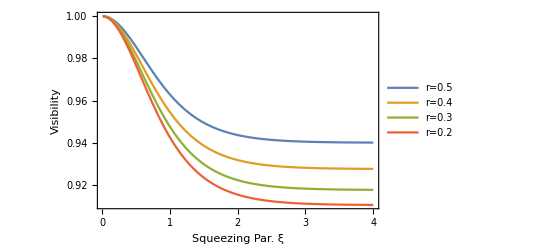

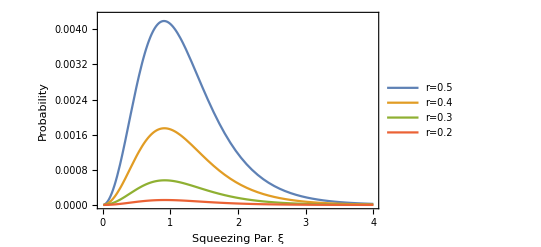

```mathematica
Plot[{Vwo2[0.5,ξ],Vwo2[0.4,ξ],Vwo2[0.3,ξ],Vwo2[0.2,ξ]},{ξ,0.01,4},PlotRange->Full,Frame->True,FrameLabel->{"Squeezing Par. ξ","Visibility","Vis. w/o Post-selection"},PlotLegends->{"r=0.5","r=0.4","r=0.3","r=0.2"},LabelStyle->Large,ImageSize->Scaled[0.25]]
Plot[{wopostselect2[0,0.5,ξ],wopostselect2 [0,0.4,ξ],wopostselect2[0,0.3,ξ],wopostselect2[0,0.2,ξ]},{ξ,0.01,4},PlotRange->{0,0.0043},Frame->True,FrameLabel->{"Squeezing Par. ξ","Probability","Max Prob. of Success w/o Post-selection"},PlotLegends->{"r=0.5","r=0.4","r=0.3","r=0.2"},LabelStyle->Large,ImageSize->Scaled[0.30]]
```

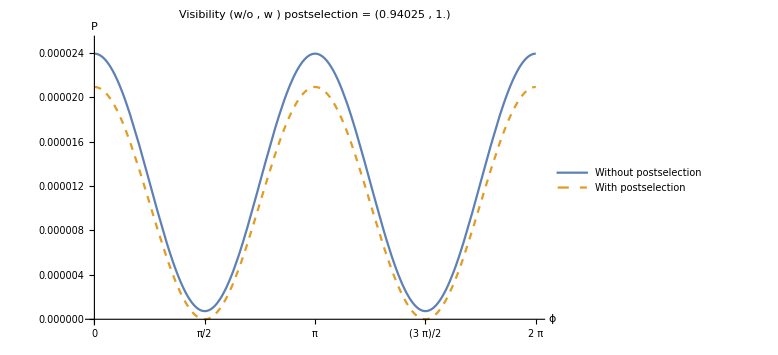

```mathematica
ClearAll[𝓇,ξ]
𝓇=0.5;
ξ=4;
Plot[{wopostselect2[ϕ,𝓇,ξ],wpostselect2[ϕ,𝓇,ξ]},{ϕ,0,2π},PlotLabel-> "Visibility (w/o , w ) postselection = ("<>ToString[Vwo2[𝓇,ξ]]<>" , "<>ToString[Vw2[𝓇,ξ]]<>")",AxesLabel-> {ϕ,P},PlotLegends->{"Without postselection","With postselection"},PlotStyle-> {Solid,Dashed},PlotRange->{0,2.5 10^-5},Ticks->{{0,π/2,π,(3π)/2,2π},Automatic},ImageSize->Large]
ClearAll[𝓇,ξ]
```

## 3. Photon number state

### Starting with number states in mode a

```mathematica
(* Photon number was mentioned in the initialization *)
ClearAll[n,out3,a,b,c,d,wopostselect3,wpostselect3]
a=0;  (* postselection on mode a *)
b=1;  (* postselection on mode b *)
c=2; (* amplitude for mode c chosen to observe the interference  *)
d=2;(* amplitude for mode d chosen to observe the interference  *)

(* Be careful when postselecting, total photons detected finally cannot be greater than the input photon number *)
n=a+b+c+d;
out3[ca2_,cb3_]=(ca0)^n/(√(n!));
```

### Observing interference with and without postselection on modes a and b

```mathematica
wopostselect3[ϕ_,𝓇_,ξ_] = Module[{coeffψ,coefftable},
𝓉=√(1-𝓇^2);
coeffψ =1/(√(c!d!))CoefficientList[CoefficientList[out3[ca,cb],{cc3,cd3}][[c+1,d+1]],{ca,cb}];
coefftable=Table[Abs[1/(√((i-1)!   (j-1)!))coeffψ[[i,j]]]^2,{i,1,Dimensions[coeffψ][[1]]},{j,1,Dimensions[coeffψ][[2]]}];
Total[Total[coefftable]]
];
wpostselect3[ϕ_,𝓇_,ξ_]=Module[{},
𝓉=√(1-𝓇^2);
Abs[1/(√(c!d! a!b!))CoefficientList[CoefficientList[out3[ca,cb],{cc3,cd3}][[c+1,d+1]],{ca,cb}][[a+1,b+1]]]^2
];
(* Visibility *)
Vwo3[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=FindMaximum[wopostselect3 [x,𝓇,ξ],{x,3 π/4}][[1]];
Imin = FindMinimum[wopostselect3 [x,𝓇,ξ],{x,3 π/4}][[1]];
N[(Imax-Imin)/(Imax+ Imin)]
];
Vw3[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=FindMaximum[wpostselect3 [x,𝓇,ξ],{x,3 π/4}][[1]];
Imin = FindMinimum[wpostselect3 [x,𝓇,ξ],{x,3 π/4}][[1]];
N[(Imax-Imin)/(Imax+ Imin)]
];
Manipulate[Plot[{wopostselect3 [ϕ,𝓇,ξ],wpostselect3[ϕ,𝓇,ξ]},{ϕ,0,2π},PlotLabel-> "Visibility (w/o , w ) postselection = ("<>ToString[Vwo3[𝓇,ξ]]<>" , "<>ToString[Vw3[𝓇,ξ]]<>")",AxesLabel-> {ϕ,P},PlotLegends->{"Without postselection","With postselection"},PlotStyle-> {Solid,Dashed},PlotRange->Full,ImageSize->Medium,Ticks->{{0,π/2,π,(3π)/2,2π},Automatic}],{𝓇,0.1,1,Appearance-> "Open"}]
```

## 4. Two-Mode Squeezed Vacuum Input and observing interference for P(coincidence w/o PNR) = P(not 0,not 0) = P(any,any)-P(0,any)-P(any,0)+P(0,0)

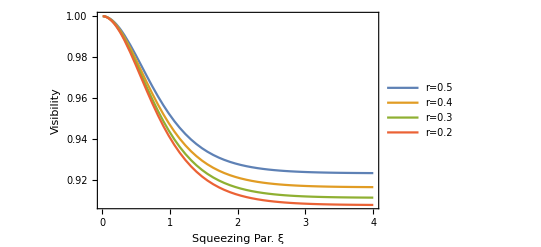

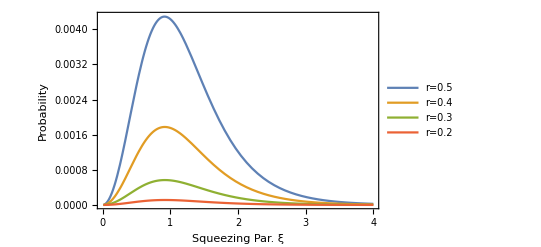

```mathematica
(* T[ξ_,n_]=1/Cosh[ξ]∑_(k=0)^n (-Tanh[ξ]/2)^k(ca0^k cb0^k)/(k!); (* Source: Wikipedia*)*)
(* T[ξ,n] approximates two mode squeezed vacuum up to photon number = n,n *)
ClearAll[out4,n]
n=5;
out4[ca2_,cb3_]=1/Cosh[ξ] Sum[(-Tanh[ξ]/2 ca0 cb0)^k/k!,{k,0,n}];
(* Approximation of taking only a few terms *)
ClearAll[wopscoin,wpscoin,a,b,c,d]
a=0;  (* postselection on mode a *)
b=0;  (* postselection on mode b *)
(*c=1; (* amplitude for mode c chosen to observe the interference  *)
d=1;(* amplitude for mode d chosen to observe the interference  *)*)
wopscoin[ϕ_,𝓇_,ξ_]=Module[{ψp,ψ,P},
𝓉=√(1-𝓇^2);
(*ψp=CoefficientList[out4[ca,cb],{cc3,cd3}];*)
ψp=CoefficientList[out4[ca,cb],{cc3,cd3,ca,cb}];
ψ =Table[ψp[[k,l]]/(√((k-1)!(l-1)!)),{k,1,Dimensions[ψp][[1]]},{l,1,Dimensions[ψp][[2]]}];
P=Table[Total[Total[Table[Abs[(ψ[[k,l]][[i,j]])/(√((i-1)!(j-1)!))]^2,{i,1,Dimensions[ψ[[k,l]]][[1]]},{j,1,Dimensions[ψ[[k,l]]][[1]]}]]],{k,1,Dimensions[ψ][[1]]},{l,1,Dimensions[ψ][[2]]}];
Total[Total[P]]-Total[P,{1}][[1]]-Total[P,{2}][[1]]+P[[1,1]]
];
wpscoin[ϕ_,𝓇_,ξ_]=Module[{ψp,ψ,P},
𝓉=√(1-𝓇^2);
ψp=CoefficientList[out4[ca,cb],{cc3,cd3,ca,cb}];
ψ =Table[ψp[[k,l]]/(√((k-1)!(l-1)!)),{k,1,Dimensions[ψp][[1]]},{l,1,Dimensions[ψp][[2]]}];
P=Table[Abs[(ψ[[k,l]][[a+1,b+1]])/(√(a!b!))]^2,{k,1,Dimensions[ψ][[1]]},{l,1,Dimensions[ψ][[2]]}];
Total[Total[P]]-Total[P,{1}][[1]]-Total[P,{2}][[1]]+P[[1,1]]
];
(* Visibility *)
Vwocoin[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=wopscoin [0,𝓇,ξ];
Imin =wopscoin [Pi/2,𝓇,ξ];
N[(Imax-Imin)/(Imax+ Imin)]
];
Vwcoin[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=wpscoin [0,𝓇,ξ];
Imin =wpscoin [Pi/2,𝓇,ξ];
N[(Imax-Imin)/(Imax+ Imin)]
];
Plot[{Vwocoin[0.5,ξ],Vwocoin[0.4,ξ],Vwocoin[0.3,ξ],Vwocoin[0.2,ξ]},{ξ,0.01,4},PlotRange->Full,Frame->True,FrameLabel->{"Squeezing Par. ξ","Visibility","Vis. w/o Post-selection"},PlotLegends->{"r=0.5","r=0.4","r=0.3","r=0.2"},LabelStyle->Large,ImageSize->Scaled[0.25]]
Plot[{wopscoin[0,0.5,ξ],wopscoin [0,0.4,ξ],wopscoin[0,0.3,ξ],wopscoin[0,0.2,ξ]},{ξ,0.01,4},PlotRange->{0,0.0043},Frame->True,FrameLabel->{"Squeezing Par. ξ","Probability","Max Prob. of Success w/o Post-selection"},PlotLegends->{"r=0.5","r=0.4","r=0.3","r=0.2"},LabelStyle->Large,ImageSize->Scaled[0.30]]
```

{0.000747601,{𝓇→0.843123,ξ→1.14562}}

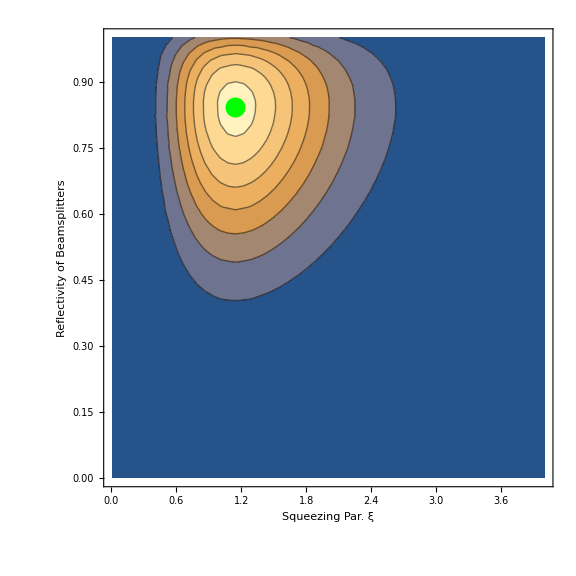

```mathematica
ClearAll[𝓇,ξ]
{val,sub}=FindMaximum[{wopscoin[0,𝓇,ξ](1-Vwocoin[𝓇,ξ]),0≤ 𝓇≤1&&0.01≤ξ≤ 4},{𝓇,0.8},{ξ,1}]
ξ=4;
ContourPlot[wopscoin[0,𝓇,ξ](1-Vwocoin[𝓇,ξ]),{ξ,0.01,4},{𝓇,0,1},FrameLabel-> {"Squeezing Par. ξ","Reflectivity of Beamsplitters","Probability ×(1-Visibility)"},Frame-> True,PlotRange->Full,Epilog->{PointSize[0.025],Green,Point[{ξ/.sub,𝓇/.sub}]},ImageSize->Large,LabelStyle->Large]
ClearAll[𝓇,ξ]
```

```mathematica
wopscoin[0,𝓇,ξ]/.sub
```

0.0296051

```mathematica
Vwocoin[𝓇,ξ]/.sub
```

0.974748

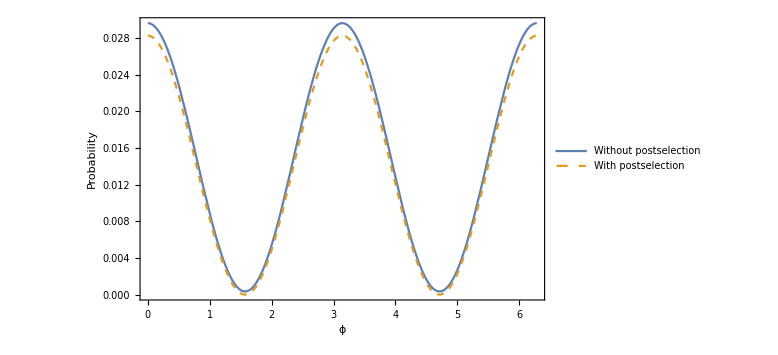

```mathematica
ClearAll[𝓇,ξ]
𝓇=𝓇/.sub;
ξ=ξ/.sub;
Plot[{wopscoin[ϕ,𝓇,ξ],wpscoin[ϕ,𝓇,ξ]},{ϕ,0,2π},FrameLabel-> {"ϕ","Probability","Visibility (w/o , w ) postselection = ("<>ToString[Vwocoin[𝓇,ξ]]<>" , "<>ToString[Vwcoin[𝓇,ξ]]<>")"},Frame-> True,PlotLegends->{"Without postselection","With postselection"},PlotStyle-> {Solid,Dashed},PlotRange->Full,Ticks->{{0,π/2,π,(3π)/2,2π},Automatic},ImageSize->Large,LabelStyle->Large]
```